## Question 6

## Part A

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]=4λ x(1-x);
```

```mathematica
λ=.1;NestList[f,0.5,10]
```

{0.5,0.1,0.036,0.0138816,0.00547556,0.00217823,0.000869395,0.000347456,0.000138934,0.0000555659,0.0000222251}

```mathematica
λ=0.2;
g1=ListPlot[{NestList[f,0.5,10],NestList[f,0.5,10]},Joined->{True,False},PlotLabel->"λ = .2"];
```

```mathematica
λ =0.4;
```

```mathematica
g2=ListPlot[{NestList[f,0.5,10],NestList[f,0.5,10]},Joined->{True,False},PlotLabel->"λ = .4"];
```

```mathematica
λ =0.6;
```

```mathematica
g3=ListPlot[{NestList[f,0.5,10],NestList[f,0.5,10]},Joined->{True,False},PlotLabel->"λ = .6"];
```

```mathematica
λ =0.8;
```

```mathematica
g4=ListPlot[{NestList[f,0.5,10],NestList[f,0.5,10]},Joined->{True,False},PlotLabel->"λ = .8"];
```

```mathematica
λ =0.84;
```

```mathematica
g5=ListPlot[{NestList[f,0.5,10],NestList[f,0.5,10]},Joined->{True,False},PlotLabel->"λ = .84"];
```

```mathematica
λ=.9;
```

```mathematica
g6=ListPlot[{NestList[f,0.5,10],NestList[f,0.5,10]},Joined->{True,False},PlotLabel->"λ = .9"];
```

```mathematica
λ =0.961;
```

```mathematica
g7=ListPlot[{NestList[f,0.5,10],NestList[f,0.5,10]},Joined->{True,False},PlotLabel->"λ = .961"];
```

```mathematica
λ =0.97;
```

```mathematica
g8=ListPlot[{NestList[f,0.5,10],NestList[f,0.5,10]},Joined->{True,False},PlotLabel->"λ = .97"];
```

```mathematica
λ =1.0;
```

```mathematica
g9=ListPlot[{NestList[f,0.5,10],NestList[f,0.5,10]},Joined->{True,False},PlotLabel->"λ = 1.0"];
```

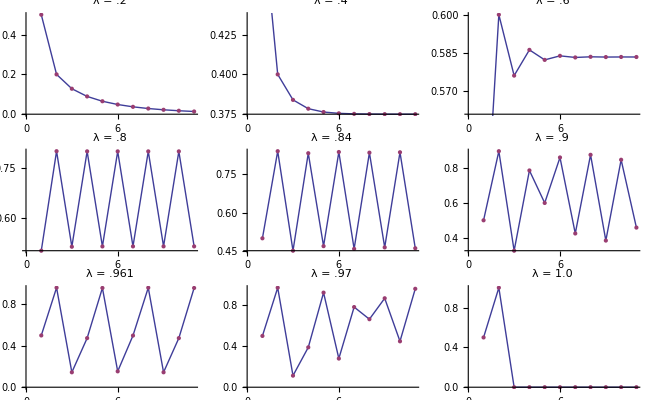

```mathematica
Show[GraphicsGrid[{{g1,g2,g3},{g4,g5,g6},{g7,g8,g9}}]]
```

```mathematica
Part B
```

B Part

```mathematica
Clear[λ]
```

```mathematica
lya[l_,xinit_,n_,ndrop_]:=( λ=l;xlist=Drop[NestList[f,xinit,n],ndrop+1]; Apply[Plus,Log[Abs[f'[xlist]]]/Length[xlist]])
```

```mathematica
lya[ .2,.7,50000,20 ]
```

-0.223144

Since this value is negative the value of x converge to an attractor in this case a fix point

```mathematica
lya[ .6,.7,50000,20 ]
```

-0.916291

Since this value is negative the value of x converge to an attractor in this case a fix point

```mathematica
lya[ .8,.7,50000,20 ]
```

-0.91629

Since this value is negative the value of x converge to an attractor in this case  lmite cyle of two

```mathematica
lya[ .84,.7,50000,20 ]
```

-0.281411

Since this value is negative the value of x converge to an attractor in this case a limit cycle of two

```mathematica
lya[ .9,.7,50000,20 ]
```

0.18411

Since this value is positive the value of x  are chaotic which is evident in the graph

```mathematica
lya[ .961,.7,50000,20 ]
```

-0.280341

Since this value is negative the value of x converge to an attractor in this case a limit cycle of two, which is interesting break inbetween chaotic regions

```mathematica
lya[ .97,.7,50000,20 ]
```

0.465007

Since this value is positive the value of x  are chaotic which is evident in the graph

```mathematica
lya[ 1.0,.7,50000,20 ]
```

0.693132

This is also choatic

## Part C

```mathematica
f5[x_]= f[f[f[f[f[x]]]]];
```

```mathematica
λ=.9345;
```

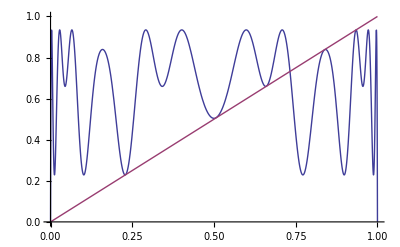

```mathematica
Plot[{f5[x],x},{x,0,1}]
```

We see that the function that the 5 cycle function is intersected 5 times and therefore must occur at this lambda

```mathematica
Part D
```

```mathematica
iterate[m_,n_]:=Drop[NestList[f,.5,n],m]
```

```mathematica
drawpt[y_]:=Point[{λ,y}]
```

```mathematica
graph[λmin_,λmax_, nλ_,mdrop_,n_] :=Graphics[{PointSize[.001],Table[Map[drawpt,iterate[mdrop,n]],{ λ,λmin,λmax,(λmax-λmin)/nλ}]}]
```

```mathematica
Show[graph[.9352,.9358,400,300,700],Axes->False,Frame->True,AspectRatio->1,PlotRange->{.48,.51}]
```

-Graphics-

## Part E

```mathematica
Clear[λ]
```

```mathematica
f2[x_] = f[f[x]];
```

```mathematica
λ /.N[Solve[{f2[x]==x,f2'[x]==-1},{x,λ}]]
```

{0.-0.25 ⅈ,0.+0.25 ⅈ,0.5-0.25 ⅈ,0.5+0.25 ⅈ,-0.362372,-0.362372,0.862372,0.862372}

```mathematica
λ2 = 0.8623724356957945;
```

```mathematica
Clear[λ,x]
```

```mathematica
f4[x_] = f2[f2[x]];
```

```mathematica
λ3 = λ/.FindRoot[{f4[x]==x,f4'[x]==-1},{x,.88},{λ,.9}]
```

0.886023

```mathematica
Clear[λ,x]
```

```mathematica
f8[x_]=f4[f4[x]];
```

```mathematica
λ4 =λ /.FindRoot[{f8[x]==x,f8'[x]==-1},{x,.88},{λ,.9}]
```

0.891102

```mathematica
(Out[305]- 0.8623724356957945)/(Out[316]-Out[305])
```

4.65625

```mathematica
δ = (λ3 -λ2)/(λ4-λ3)
```

4.65625

Which is close the value expected

## Question 7

```mathematica
Clear[λ,x,lya]
```

```mathematica
g[x_]= λ Sin[Pi x]
```

λ Sin[π x]

```mathematica
lya[l_,xinit_,n_,ndrop_]:=( λ=l;xlist=Drop[NestList[g,xinit,n],ndrop+1]; Apply[Plus,Log[Abs[g'[xlist]]]/Length[xlist]]);
```

```mathematica
lya[.9,.7,50000,20]
```

0.349435

```mathematica
λ=N[9/10,10000];x0=N[4/10,10000];
```

```mathematica
NumberForm[N[Nest[g,x0,5000],10000],5]
```

0.79559

x5000 = .79559;  This value has 10, 000 digits or precision